```mathematica
a[n_]=(1+1/n)^n
```

(1+1/n)^n

```mathematica
a[1]
```

2

```mathematica
N[a[10],20]
```

2.5937424601

```mathematica
N[a[100],20 ]
```

2.7048138294215260933

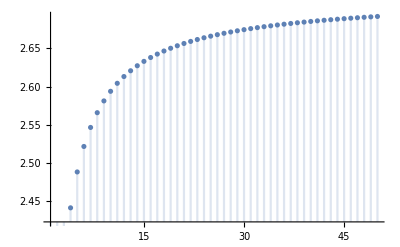

```mathematica
DiscretePlot[a[n],{n, 1, 50}]
```

```mathematica
Limit[a[n],n-> Infinity]
```

ⅇ

```mathematica
N[E,20]
```

2.7182818284590452354

```mathematica
N[a[1000],20]
```

2.7169239322358924574

```mathematica
b[n_]= Sum[1/k!,{k,0,n}]
```

(ⅇ Gamma[1+n,1])/Gamma[1+n]

```mathematica
Limit[b[n],n->Infinity]
```

```mathematica
N[ⅇ,20]
```

2.7182818284590452354

```mathematica
N[b[10],20]
```

2.7182818011463844797

```mathematica
N[b[20],20]
```

2.7182818284590452353

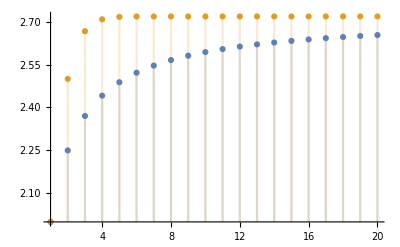

```mathematica
DiscretePlot[{a[n],b[n]},{n,1,20}]
```

```mathematica
Limit[((2n+1)/(2n-Sqrt[n]))^Sqrt[n+2],n-> Infinity]
```

√ⅇ

```mathematica
Limit[Sum[k^2,{k,1,n}]/n^3,n->Infinity]
```

1/3

```mathematica
Limit[{Sqrt[n^5]-Sqrt[n^3+1]/Log[n]},n->Infinity]
```

{∞}

```mathematica
Limit[E^n,n-> Infinity]
```

∞

```mathematica
Limit[n^2/Sqrt[n^3],n-> Infinity]
```

∞

```mathematica
Limit[n^2/Log[n],n-> Infinity]
```

∞

```mathematica
Limit[n^2/E^n,n-> Infinity]
```

0

```mathematica
Limit[n/Log[n],n-> Infinity]
```

∞

```mathematica
Limit[Sqrt[n^5+2]-Sqrt[n^4-1],n-> Infinity]
```

∞

```mathematica
c[n_]=Sqrt[n^5+2]-Sqrt[n^4-1]
```

-√(-1+n^4)+√(2+n^5)

```mathematica
Limit[c[n]/n^2,n-> Infinity]
```

∞

```mathematica
Limit[c[n]/n^3,n-> Infinity]
```

0

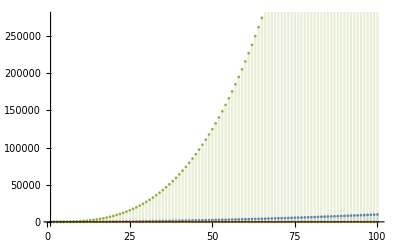

```mathematica
DiscretePlot[{n^2,a[n],n^(2+1)},{n,1,100}]
```

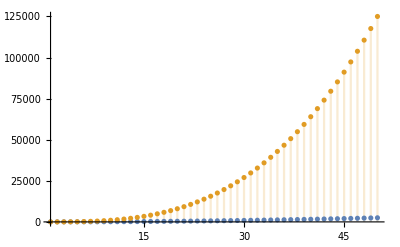

```mathematica
DiscretePlot[{n^2,n^(2+1)},{n,1,50}]
```

```mathematica
3
```